```mathematica
h0 =-m{{0,(px-I py)^2},{(px+I py)^2,0}}; (*m depends only on gamma0, gamma3*)
hw =v3{{0,(px + I py)},{(px - I py), 0}} ; (* v3 depends only on gamma3*)
H = Simplify[h0 + hw];
GIm = Inverse[I ω PauliMatrix[0] - H];
asslist = {Element[m,Reals],Element[v3,Reals], Element[px,Reals],v3>0,m>0};
Simplify[GIm[[1,1]]]
```

-(ⅈ ω)/(m^2 (px^2+py^2)^2-2 m px (px^2-3 py^2) v3+px^2 v3^2+py^2 v3^2+ω^2)

```mathematica
gKxy = FullSimplify[Integrate[-(ω + I η)/(m^2 (px^2+py^2)^2-2 m px (px^2-3 py^2) v3+px^2 v3^2+py^2 v3^2-(ω + I η)^2),{py,-Infinity,Infinity},GenerateConditions->False],Assumptions->asslist]
```

-(π (m √(1/(2 m^2 px^2+6 m px v3+v3^2-√(32 m^3 px^3 v3+12 m px v3^3+v3^4+4 m^2 (9 px^2 v3^2-(η-ⅈ ω)^2))))-m √(1/(2 m^2 px^2+6 m px v3+v3^2+√(32 m^3 px^3 v3+12 m px v3^3+v3^4+4 m^2 (9 px^2 v3^2-(η-ⅈ ω)^2))))) (ⅈ η+ω))/(√(16 m^3 px^3 v3+6 m px v3^3+v3^4/2+2 m^2 (9 px^2 v3^2-(η-ⅈ ω)^2)))

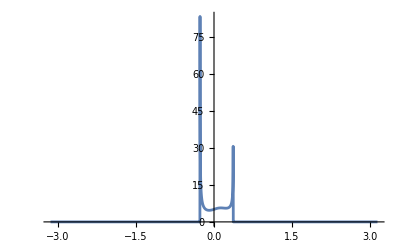

```mathematica
Plot[-Im[gKxy/.{m->1, v3->0.1, η-> 0.000000001,ω->0.1}], {px,-Pi,Pi},PlotRange->Full]
```

```mathematica
NIntegrate[-Im[gKxy/.{m->1, v3->0.1, η-> 0.00001,ω->0.001}], {px,-Infinity,Infinity},Method->"GlobalAdaptive",MinRecursion->1,MaxRecursion->1000,AccuracyGoal->6, IntegrationMonitor :>((errors=Through[#1@"Error"])&)]
Length@errors
Total@errors
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

2.07893

88

2.00699×10^-6

```mathematica
gKxy
```

-(π (m √(1/(2 m^2 px^2+6 m px v3+v3^2-√(32 m^3 px^3 v3+12 m px v3^3+v3^4+4 m^2 (9 px^2 v3^2-(η-ⅈ ω)^2))))-m √(1/(2 m^2 px^2+6 m px v3+v3^2+√(32 m^3 px^3 v3+12 m px v3^3+v3^4+4 m^2 (9 px^2 v3^2-(η-ⅈ ω)^2))))) (ⅈ η+ω))/(√(16 m^3 px^3 v3+6 m px v3^3+v3^4/2+2 m^2 (9 px^2 v3^2-(η-ⅈ ω)^2)))

```mathematica
strreprule = {"Pi"-> "np.pi", "Sqrt"->"cmath.sqrt", "η"->"eta", "Arg"->"np.angle", "Floor"->"np.floor", "ω"->"omega","Im"->"np.imag" };
```

```mathematica
StringReplace[(-1/Pi Im[gKxy]//FortranForm //ToString //StringReplace[strreprule]), RegularExpression["\\(0,([^()]+)\\)"] :> "$1j"]
```

np.imag(((m*cmath.sqrt(1/(2*m**2*px**2 + 6*m*px*v3 + v3**2 - cmath.sqrt(32*m**3*px**3*v3 + 12*m*px*v3**3 + v3**4 + 4*m**2*(9*px**2*v3**2 - (eta - 1j*omega)**2)))) - m*cmath.sqrt(1/(2*m**2*px**2 + 6*m*px*v3 + v3**2 + cmath.sqrt(32*m**3*px**3*v3 + 12*m*px*v3**3 + v3**4 + 4*m**2*(9*px**2*v3**2 - (eta - 1j*omega)**2)))))*(1j*eta + omega))/cmath.sqrt(16*m**3*px**3*v3 + 6*m*px*v3**3 + v3**4/2. + 2*m**2*(9*px**2*v3**2 - (eta - 1j*omega)**2)))